```mathematica
DimOfHilbertSpace=4;
t1=1;
t2=1/Sqrt[2];

randSym[n_]:=Module[{uptri=Table[If[i>j,RandomVariate[UniformDistribution[{-1,1}]],0],{i,1,n},{j,1,n}],diag=DiagonalMatrix[RandomVariate[UniformDistribution[{-1,1}],n]]},diag+uptri+Transpose[uptri]]
Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}};
Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}};
ω1=2.1;
ω2=2.7;
H[t_]= ((Sin[t/t1] ω1+Sin[t/t2])*Hinitial+(Cos[t/t1] ω2+Cos[t/t2])*Hend);
DHT[t_]=D[H[t],t];
ESystem[t_]:=Eigensystem[H[t]];
EValueSystemOrder[t_]:=Sort[ESystem[t][[1,All]],Less];
order[t_]:=Table[Flatten[Position[EValueSystemOrder[t],ESystem[t][[1,i]]]][[1]],{i,1,DimOfHilbertSpace}];

ESystemOrdered[t_]:=Permute[ESystem[t][[2]],order[t]]
```

#### FindError Module

```mathematica
FindError[Tscale_,endTime_]:=Module[{sol},sol=X[t]/.NDSolve[{I D[X[t],t]==Tscale* Dot[H[t],X[t]],X[0.00]==ESystemOrdered[0.00][[1]]},{X[t]},{t,0,endTime}]//Simplify;
NormalizedSol[x_]:=((sol/.{t->x})[[1]])/Sqrt[Sum[((sol/.{t->x})[[1,i]])*Conjugate[((sol/.{t->x})[[1,i]])],{i,1,DimOfHilbertSpace}]];
InstantaneousGSPopulation[t_]:=(N[Norm[ESystemOrdered[t][[1]]]])^(-2)(Dot[NormalizedSol[t],ESystemOrdered[t][[1]]])*Conjugate[(Dot[NormalizedSol[t],ESystemOrdered[t][[1]]])];Sqrt[1-InstantaneousGSPopulation[endTime]]]
```

#### Find PathLength Module

```mathematica
FindPLength[endTime_]:=Module[{},GroundStateIntDif[x_]:=Normalize[{1,ESystemOrdered[x][[1,2]]*(ESystemOrdered[x][[1,1]]^(-1)),ESystemOrdered[x][[1,3]]*(ESystemOrdered[x][[1,1]]^(-1)),ESystemOrdered[x][[1,4]]*(ESystemOrdered[x][[1,1]]^(-1))}];
ESystemOrderedPhaseCont[x_,i_]:=Normalize[{1,ESystemOrdered[x][[i,2]]*(ESystemOrdered[x][[i,1]]^(-1)),ESystemOrdered[x][[i,3]]*(ESystemOrdered[x][[i,1]]^(-1)),ESystemOrdered[x][[i,4]]*(ESystemOrdered[x][[i,1]]^(-1))}];
inf=endTime/1000;
DGSbySVector[y_]:=(*ND[GroundStateDifInt[x],x,y,Scale->(t1/1000)]*)Table[(GroundStateIntDif[y+inf][[i]]-GroundStateIntDif[y][[i]])/inf,{i,1,DimOfHilbertSpace}];
PathLengthIntegrand[t_]:=Norm[DGSbySVector[t](*-GroundStateIntDif[t](Dot[Conjugate[DGSbySVector[t]],GroundStateIntDif[t]])*)];
PathLengthIntegrandInt:=Interpolation[Table[{t,PathLengthIntegrand[t]},{t,0.00,endTime,(endTime)/20}]];
PathLength:= NIntegrate[PathLengthIntegrandInt[t],{t,0.00,endTime}];PathLength]
```

```mathematica
FindPLength[200]
```

303.435

```mathematica
FindError[42,200]
```

0.0143698-1.93153×10^-15 ⅈ

#### Find Estimated Error Module

```mathematica
Abst1=AbsoluteTime[];
FindEstimatedError[Tscale_,endTime_]:=Module[{},GroundStateIntDif[x_]:=Normalize[{1,ESystemOrdered[x][[1,2]]*(ESystemOrdered[x][[1,1]]^(-1)),ESystemOrdered[x][[1,3]]*(ESystemOrdered[x][[1,1]]^(-1)),ESystemOrdered[x][[1,4]]*(ESystemOrdered[x][[1,1]]^(-1))}];
ESystemOrderedPhaseCont[x_,i_]:=Normalize[{1,ESystemOrdered[x][[i,2]]*(ESystemOrdered[x][[i,1]]^(-1)),ESystemOrdered[x][[i,3]]*(ESystemOrdered[x][[i,1]]^(-1)),ESystemOrdered[x][[i,4]]*(ESystemOrdered[x][[i,1]]^(-1))}];
EnergyDifferenceBetweenStates[t_,i_]:=(EValueSystemOrder[t][[i]]-EValueSystemOrder[t][[1]]);
ExcitedStateDotHDTDotGS[t_,i_]:=(N[Norm[ESystemOrderedPhaseCont[t,1]]])^(-1)(N[Norm[ESystemOrderedPhaseCont[t,i]]])^(-1)Dot[Conjugate[ESystemOrderedPhaseCont[t,i]],Dot[DHT[t],ESystemOrderedPhaseCont[t,1]]];
EValueSystemOrderInt=Table[Interpolation[Table[{x,EValueSystemOrder[x][[i]]},{x,0.00,endTime,endTime/100}]],{i,1,DimOfHilbertSpace}];
PhaseFac[t_,i_]:=Exp[Tscale*I *NIntegrate[EValueSystemOrderInt[[i]][x]-EValueSystemOrderInt[[1]][x],{x,0.00,t}]];


OverlapFormula[t_]:=(Cos[(Tscale)^(-1)Sqrt[Sum[(Abs[(PhaseFac[t,i]*ExcitedStateDotHDTDotGS[t,i]/(EnergyDifferenceBetweenStates[t,i])^2)-(PhaseFac[0.00,i]*ExcitedStateDotHDTDotGS[0.00,i]/(EnergyDifferenceBetweenStates[0.00,i])^2)])^2,{i,2,DimOfHilbertSpace}]]])^2;
InstantaneousGSPopulation[t_]:=(N[Norm[GroundStateIntDif[t]]])^(-2)(Dot[NormalizedSol[t],GroundStateIntDif[t]])*Conjugate[(Dot[NormalizedSol[t],GroundStateIntDif[t]])];
errorFormula[t_]:=1-OverlapFormula[t];Return[Sqrt[errorFormula[endTime]]]]
Print["TimeTaken5",AbsoluteTime[]-Abst1]
```

TimeTaken50.005556

```mathematica
FindEstimatedError[5000,4000]
```

0.0000471814

#### Analysis of Data Imported from Prudence

```mathematica
SetDirectory["/Users/maneeshasushamapradeep/Documents/StudyAtUMD/AdiabaticStatePreparation/"]
```

/Users/maneeshasushamapradeep/Documents/StudyAtUMD/AdiabaticStatePreparation

```mathematica
T1=Import["ErrorTable.dat"]; (*Imports my saved table containing error for each Tscale and end time*)
```

```mathematica
T2=ToExpression[StringReplace[ToString[T1],",,"->","]];
```

```mathematica
FindTScaleForGivenEndTimeAndError[EndTime_,Error_]:=Module[{T2a,T2b,EndTime1=((EndTime+9)/10)},T2a=Select[T2[[All,EndTime1,2]],#<Error&];
T2b=Table[Position[T2[[All,EndTime1,2]],T2a[[i]]][[1,1]],{i,1,Length[T2a]}];T2[[Module[{t1=0,t2},For[i=1,i<=Length[T2b],i=i+1,If[T2b[[i]]==T2b[[i-1]]+1,Continue, t1=T2b[[i]]];];t1],EndTime1,1,1]]]
```

```mathematica
FindTScaleForGivenEndTimeAndError[201,0.1](*Can input endtime values in the table only*)
```

21

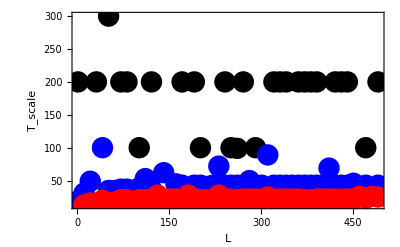

```mathematica
DiscretePlot[{FindTScaleForGivenEndTimeAndError[x,0.001],FindTScaleForGivenEndTimeAndError[x,0.01],FindTScaleForGivenEndTimeAndError[x,0.1]},{x,1,491,10},PlotRange->All,Frame->True,Filling->None,FrameLabel->{"L","T_scale"},PlotMarkers->{Style["•", FontSize -> 22,Black],Style["•", FontSize -> 22,Blue],Style["•", FontSize -> 22,Red]},LabelStyle->{18,Bold,Black}]
```

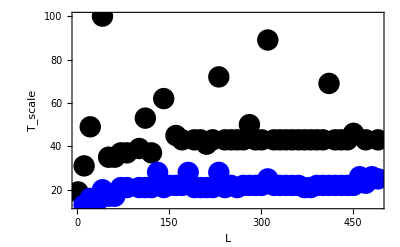

```mathematica
DiscretePlot[{FindTScaleForGivenEndTimeAndError[x,0.01],FindTScaleForGivenEndTimeAndError[x,0.1]},{x,1,491,10},PlotRange->All,Frame->True,Filling->None,FrameLabel->{"L","T_scale"},PlotMarkers->{Style["•", FontSize -> 22,Black],Style["•", FontSize -> 22,Blue],Style["•", FontSize -> 22,Red]},LabelStyle->{18,Bold,Black}]
```